```mathematica
Quit[]
```

```mathematica
fKu = x^(-1/2)* (1-x)^(3/2) (*K, u*);
fKs= x^(0)* (1-x)^(1) (*K, s*);
fKg = x^(-1)*(1-x)^(2);
fDu= x^(-1/2)* (1-x)^(9/2) (*D, u*);
fDc= x^(3)* (1-x)^(1) (*D, c*);
fDg = x^(-1)*(1-x)^(5);
fΥb = x^(+8)* (1-x)^(19/2) (*Υ, b*);
fΥg = x^(-1)* (1-x)^(37/2) (*Υ, g*);
fΩ1s =  x^(0)* (1-x)^(15/2);
fΩ1c =  x^(+3)* (1-x)^(9/2);
fΩ1g =  x^(-1)* (1-x)^(17/2);
fΩ2s =  x^(0)* (1-x)^(25/2);
fΩ2b =  x^(+8)* (1-x)^(9/2);
fΩ2g =  x^(-1)* (1-x)^(27/2);
```

```mathematica
IKu =NIntegrate[fKu, {x, 0, 1}];
IKs = NIntegrate[fKs, {x, 0, 1}];
IDu = NIntegrate[fDu, {x, 0, 1}];
IDc = NIntegrate[fDc, {x, 0, 1}];
IΥb = NIntegrate[fΥb, {x, 0, 1}];
IΩ1s =  NIntegrate[fΩ1s, {x, 0, 1}];
IΩ1c =  NIntegrate[fΩ1c, {x, 0.0, 1}];
IΩ2s =  NIntegrate[fΩ2s, {x, 0, 1}];
IΩ2b =  NIntegrate[fΩ2b, {x, 0.0, 1}];
```

```mathematica
xKu = NIntegrate[x*fKu, {x, 0, 1}]/  NIntegrate[fKu, {x, 0, 1}];
xKs = NIntegrate[x*fKs, {x, 0, 1}]/  NIntegrate[fKs, {x, 0, 1}];
 xDu = NIntegrate[x*fDu, {x, 0, 1}]/  NIntegrate[fDu, {x, 0, 1}];
xDc = NIntegrate[x*fDc, {x, 0, 1}]/  NIntegrate[fDc, {x, 0, 1}];
xΥb = NIntegrate[x*fΥb, {x, 0, 1}]/  NIntegrate[fΥb, {x, 0, 1}];
xΩ1s =  NIntegrate[x*fΩ1s, {x, 0, 1}]/  NIntegrate[fΩ1s, {x, 0, 1}];
xΩ1c =  NIntegrate[x*fΩ1c, {x, 0.0, 1}]/  NIntegrate[fΩ1c, {x, 0.0, 1}];
xΩ2s =  NIntegrate[x*fΩ2s, {x, 0, 1}]/  NIntegrate[fΩ2s, {x, 0, 1}];
xΩ2b =  NIntegrate[x*fΩ2b, {x, 0.0, 1}]/  NIntegrate[fΩ2b, {x, 0.0, 1}];
```

```mathematica
CDg = (1-xDu-xDc)/NIntegrate[x*fDg, {x, 0, 1}]
CKg = (1-xKu-xKs)/NIntegrate[x*fKg, {x, 0, 1}]
CΥg = (1-2*xΥb)/NIntegrate[x*fΥb,{x, 0, 1}]
CΩ1g=(1-xΩ1c -2*xΩ1s)/NIntegrate[x*fΩ1g,{x,0,1}]
CΩ2g=(1-xΩ2b-2*xΩ2s)/NIntegrate[x*fΩ2g,{x,0,1}]
```

1.5

1.5

101124.

3.5

3.5

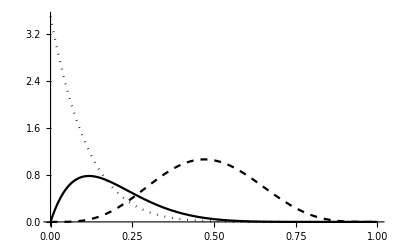

```mathematica
pic1=Show[Plot[x*2fΩ1s/IΩ1s,{x,0.0, 1}, PlotRange->All, PlotStyle-> Black],Plot[ x*fΩ1c/IΩ1c,{x,0.0, 1}, PlotRange->All, PlotStyle-> {Black,Dashed}] , Plot[x*fΩ1g*CΩ1g,{x,0.0, 1}, PlotRange->All,PlotStyle-> { Black,Dotted}]]
```

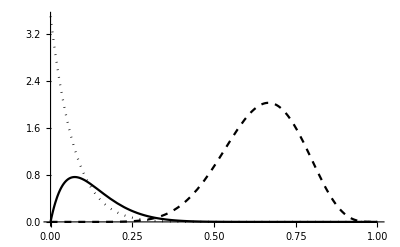

```mathematica
pic2=Show[Plot[x*2fΩ2s/IΩ2s,{x,0.0, 1}, PlotRange->All, PlotStyle-> Black],Plot[ x*fΩ2b/IΩ2b,{x,0.0, 1}, PlotRange->All, PlotStyle-> {Black,Dashed}] , Plot[x*fΩ2g*CΩ2g,{x,0.0, 1}, PlotRange->All,PlotStyle-> { Black,Dotted}]]
Plot[{x*2fΩ2s/IΩ2s, x*fΩ2b/IΩ2b,x*fΩ2g*CΩ2g},{x,0.0, 1}, PlotRange->All];
```

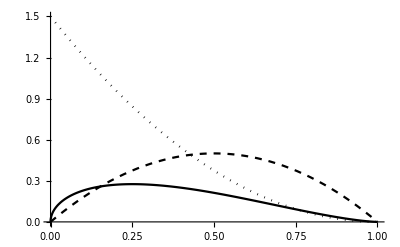

```mathematica
pic3=Show[Plot[x*fKu/IKu,{x,0.0, 1}, PlotRange->All, PlotStyle-> Black],Plot[ x*fKs/IKs,{x,0.0, 1}, PlotRange->All, PlotStyle-> {Black,Dashed}] , Plot[x*fKg*CKg,{x,0.0, 1}, PlotRange->All,PlotStyle-> { Black,Dotted}]]
Plot[{x*fKu/IKu,x*fKs/IKs, x*fKg*CKg},{x,0.0, 1}, PlotRange->All];
```

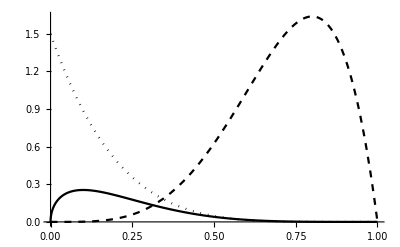

```mathematica
pic4=Show[Plot[x*fDu/IDu,{x,0.0, 1}, PlotRange->All, PlotStyle-> Black],Plot[x*fDc/IDc,{x,0.0, 1}, PlotRange->All, PlotStyle-> {Black,Dashed}] , Plot[x*fDg*CDg,{x,0.0, 1}, PlotRange->All,PlotStyle-> { Black,Dotted}]]
Plot[{x*fDu/IDu,x*fDc/IDc, x*fDg*CDg},{x,0., 1}, PlotRange->All];
```

```mathematica
SetDirectory["C:\\Users\\Tony\\Desktop\\pics"];
Export["pic1.eps", pic1];
Export["pic2.eps", pic2];
Export["pic3.eps", pic3];
Export["pic4.eps", pic4];
```

```mathematica
Plot[x*fΥb/IΥb,{x,0., 1}, PlotRange->All]
```

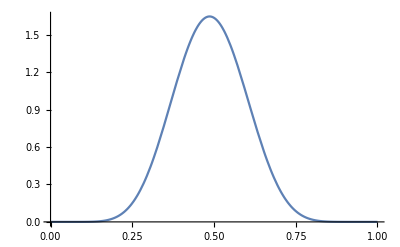
```mathematica
-Graphics-Volume 100,Issue 7
```

```mathematica
Volume 100,Issue 7
```

```mathematica
xΩ1c+2*xΩ1s
```

0.631579

```mathematica
xΩ2b+2*xΩ2s
```

0.758621

```mathematica
fΩc
```

(1-x)^(9/2) x^3

```mathematica
Volume 100,Issue 7
```

```mathematica
fπ=x^(-1/2)* (1-x)^(1);
fp=x^(-1/2)* (1-x)^(3);
Iπ=NIntegrate[fπ, {x, 0, 1}];
Ip=NIntegrate[fp, {x, 0, 1}];
xπ= NIntegrate[x*fπ, {x, 0, 1}]/NIntegrate[fπ, {x, 0, 1}];
xp=NIntegrate[x*fp, {x, 0, 1}]/NIntegrate[fp, {x, 0, 1}];
fπg=x^(-1)* (1-x)^(3/2);
fpg=x^(-1)* (1-x)^(7/2);
Cπg = (1-2*xπ)/NIntegrate[x*fπg, {x, 0, 1}];
Cpg = (1-3*xp)/NIntegrate[x*fpg, {x, 0, 1}];
xπg =Cπg* NIntegrate[x*fπg, {x, 0, 1}];
xpg = Cpg * NIntegrate[x*fpg, {x, 0, 1}];
```

```mathematica
3*xp+xpg
```

1.

```mathematica
(1-2*xπ)
(1-3*xp)
```

0.6

0.666667

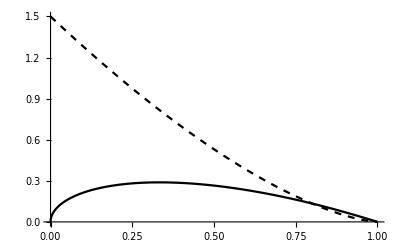

```mathematica
pic5=Show[Plot[x*fπ/Iπ,{x,0.0, 1}, PlotRange->All, PlotStyle->{Black}],Plot[x*fπg*Cπg,{x,0.0, 1}, PlotRange->All, PlotStyle->{Black, Dashed}]]
```

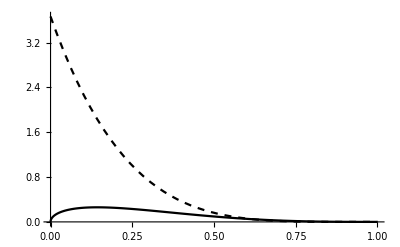

```mathematica
pic6=Show[Plot[x*fp/Ip,{x,0.0, 1}, PlotRange->All, PlotStyle->{Black}],Plot[x*fpg*Cpg,{x,0.0, 1}, PlotRange->All, PlotStyle->{Black, Dashed}]]
Plot[{x*fp/Ip,x*fpg*Cpg},{x,0.0, 1}, PlotRange->All];
```

```mathematica
Export["pic5.eps", pic5];
Export["pic6.eps", pic6];
```